```mathematica
(* ECUACIONES *)

(******************************************************************************)
(* FRECUENCIAS FASE NORMAL*)
(******************************************************************************)

Clear[ωzxn,ωzyn];
Clear[ω,ωo]
ω=1;
ωo=1;
(* ωzxn Frecuencia dependendiente z-x Fase Normal *)
ωzxn[ηz_,ηx_]:=ωo*√(1-(ηz-ηx)/ωo); 
(* ωzyn Frecuencia dependendiente z-y Fase Normal *)
ωzyn[ηz_,ηy_]:=1-(ηz-ηy)/ωo; 

(******************************************************************************)
(* FRECUENCIAS FASE SUPERRADIANTE *)
(******************************************************************************)

Clear[μx,ω1,ω2,ω3,ω4,ω5,ωzxs1,ωzxs2,ωzys1,ωzys2];
(* Resultado de eliminar términos lineales *)
μx[ηz_,ηx_,γ_,ξ_]:=1/((γ^2*(1+ξ)^2)/(ω*ωo)+(ηz-ηx)/ωo);

(* ω1 Frecuencia relacionada con d^*d *)
ω1[ηz_,ηx_,γ_,ξ_]:=1/2((ωo/μx[ηz,ηx,γ,ξ]-ηz)*(1+μx[ηz,ηx,γ,ξ])+ηx*(1-μx[ηz,ηx,γ,ξ]));


(* ω2 Frecuencia relacionada con (d^*+d)^2 *)
ω2[ηz_,ηx_,γ_,ξ_]:=1/8*(1-μx[ηz,ηx,γ,ξ])*(ωo/(1+μx[ηz,ηx,γ,ξ])*(3+μx[ηz,ηx,γ,ξ])/μx[ηz,ηx,γ,ξ]+ηz+ηx*((3*μx[ηz,ηx,γ,ξ]^2-2*μx[ηz,ηx,γ,ξ]+3)/(1-μx[ηz,ηx,γ,ξ]^2)));

(* ω3 Frecuencia relacionada con (c^*+c)(d^*+d) *)
ω3[ηz_,ηx_,γ_,ξ_]:=-(√2)/4*γ*(1+ξ)*(1-μx[ηz,ηx,γ,ξ])/Sqrt[1+μx[ηz,ηx,γ,ξ]];


(* ω4 Frecuencia relacionada con (cd^* + c^*d)(...) *)
ω4[ηz_,ηx_,γ_,ξ_]:=γ*Sqrt[1/2*(1+μx[ηz,ηx,γ,ξ])];

(* ω5 Frecuencia relacionada con (d^*-d)^2 *)
ω5[ηz_,ηx_,ηy_,γ_,ξ_]:=-1/8*ηy*(1+μx[ηz,ηx,γ,ξ]);

(* Frecuencias compuestas zx *)
ωzxs1[ηz_,ηx_,γ_,ξ_]:=ω1[ηz,ηx,γ,ξ]^2+4*ω2[ηz,ηx,γ,ξ]*ω1[ηz,ηx,γ,ξ] ;

ωzxs2[ηz_,ηx_,γ_,ξ_]:=Sqrt[ω*ω1[ηz,ηx,γ,ξ]]*(4*ω3[ηz,ηx,γ,ξ]+2*ω4[ηz,ηx,γ,ξ]*(1+ξ));

(* Frecuencias compuestas zy *)
ωzys1[ηz_,ηx_,ηy_,γ_,ξ_]:=1-(4*ω5[ηz,ηx,ηy,γ,ξ])/ω1[ηz,ηx,γ,ξ];
ωzys2[ηz_,ηx_,ηy_,γ_,ξ_]:=(2*ω4[ηz,ηx,γ,ξ]*(1-ξ))/Sqrt[ω*ω1[ηz,ηx,γ,ξ]]

(******************************************************************************)
(* Energías de oscilador *)
(******************************************************************************)

(**************************)
(* Energía del oscilador 1 *)
(***************************)

Clear[ϵ1pn,ϵ1ps,ϵ1mn,ϵ1ms];
(* Energía 1+ Fase Normal *)
ϵ1pn[ηz_,ηx_,γ_,ξ_]:=Sqrt[1/2*(ω^2+ωzxn[ηz,ηx]^2+√((ωzxn[ηz,ηx]^2-ω^2)^2+4*γ^2*ω*ωo*(1+ξ)^2))];
(* Energía 1- Fase Normal *)
ϵ1mn[ηz_,ηx_,γ_,ξ_]:=Sqrt[1/2*(ω^2+ωzxn[ηz,ηx]^2-√((ωzxn[ηz,ηx]^2-ω^2)^2+4*γ^2*ω*ωo*(1+ξ)^2))];
(* Energía 1+ Fase Superradiante *)
ϵ1ps[ηz_,ηx_,γ_,ξ_]:=Sqrt[1/2*(ω^2 + ωzxs1[ηz,ηx,γ,ξ] + Sqrt[(ωzxs1[ηz,ηx,γ,ξ] - ω^2)^2 + ωzxs2[ηz,ηx,γ,ξ]^2] )];
(* Energía 1- Fase Superradiante *)
ϵ1ms[ηz_,ηx_,γ_,ξ_]:=Sqrt[1/2*(ω^2 + ωzxs1[ηz,ηx,γ,ξ] - Sqrt[(ωzxs1[ηz,ηx,γ,ξ] - ω^2)^2 + ωzxs2[ηz,ηx,γ,ξ]^2] )];
(**************************)
(* Energía del oscilador 2 *)
(***************************)
Clear[ϵ2pn,ϵ2ps,ϵ2mn,ϵ2ms];

(* Energía 2+ Fase Normal *)
ϵ2pn[ηz_,ηy_,γ_,ξ_]:=Sqrt[1/2*(1+ωzyn[ηz,ηy]+√((ωzyn[ηz,ηy]^2-1)^2+(4*γ^2*(1-ξ)^2)/(ω*ωo)))];
(* Energía 2- Fase Normal *)
ϵ2mn[ηz_,ηy_,γ_,ξ_]:=Sqrt[1/2*(1+ωzyn[ηz,ηy]-√((ωzyn[ηz,ηy]^2-1)^2+(4*γ^2*(1-ξ)^2)/(ω*ωo)))];
(* Energía 2+ Fase Superradiante *)
ϵ2ps[ηz_,ηx_,ηy_,γ_,ξ_]:=Sqrt[1/2*(1+ωzys1[ηz,ηx,ηy,γ,ξ]+Sqrt[(ωzys1[ηz,ηx,ηy,γ,ξ]-1)^2 + ωzys2[ηz,ηx,ηy,γ,ξ]^2])];
(* Energía 2- Fase Superradiante *)
ϵ2ms[ηz_,ηx_,ηy_,γ_,ξ_]:=Sqrt[1/2*(1+ωzys1[ηz,ηx,ηy,γ,ξ]-Sqrt[(ωzys1[ηz,ηx,ηy,γ,ξ]-1)^2 +ωzys2[ηz,ηx,ηy,γ,ξ]^2])];
(*********************************************************************)
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

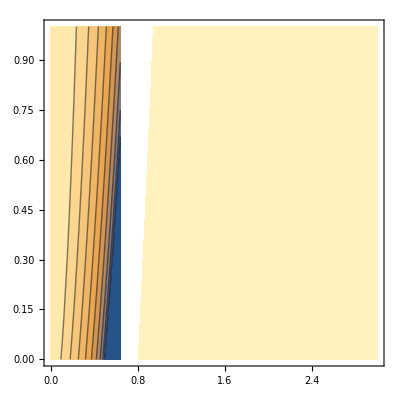

```mathematica
Clear[ξ,ηx]

p1[ηy_,ηz_,ξ_]:=ContourPlot[Re[(ϵ1mn[ηz,ηx,γ,ξ]*ϵ2mn[ηz,ηy,γ,ξ])],{γ,0,3},{ηx,0,1},RegionFunction->Function[{ηx,γ},ηx<Sqrt[(ω*ωo)/(1+ξ)^2 (1-(ηz-ηx)/ωo)]]]

p2[ηy_,ηz_,ξ_]:=ContourPlot[Re[(ϵ1ms[ηz,ηx,γ,ξ]*ϵ2ms[ηz,ηx,ηy,γ,ξ])],{γ,0,3},{ηx,0,1},RegionFunction->Function[{ηx,γ},ηx>Sqrt[(ω*ωo)/(1+ξ)^2 (1-(ηz-ηx)/ωo)]]]
Show[p1[0,0,1],p2[0,0,1]]
```

```mathematica
p2[ηy_,ηz_,ξ_]:=ContourPlot[Re[(ϵ1ms[ηz,ηx,γ,ξ]*ϵ2ms[ηz,ηx,ηy,γ,ξ])],{γ,0,3},{ηx,0,1},RegionFunction->Function[{ηx,γ},ηx>Sqrt[(ω*ωo)/(1+ξ)^2 (1-(ηz-ηx)/ωo)]]]
```